```mathematica
file1=<<"/Users/ruppell/Math/temp/outNMSSM.txt";
file2=<<"/Users/ruppell/Math/temp/output2.txt";
file3=<<"/Users/ruppell/Math/temp/cs-2.txt";
```

{Omega, MG1, Mcdm, bB, cC, hh, ww, zz}

```mathematica
file2[[1,6]]//TableForm
```

0.0312
~o1
26

```mathematica
(*For plotting against neutralino mass*)
xaxel2=file2[[;;,3,1,1]];
xaxel1=file1[[;;,3]];
xaxel3=file3[[;;,3]];
```

```mathematica
(*For plotting against M1*)
xaxel1=file1[[;;,2]];
xaxel3=file3[[;;,2]];
xaxel2=file2[[;;,2,1]];
```

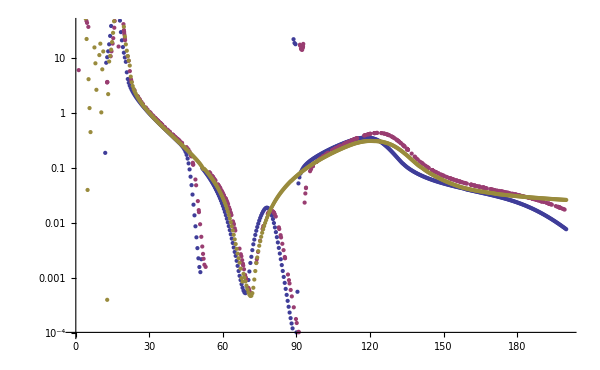

```mathematica
yaxel1=file1[[;;,1]];
yaxel3=file3[[;;,1]];
yaxel2=file2[[;;,6,1]];
ListLogPlot[{Transpose@{xaxel1,yaxel1},Transpose@{xaxel2,yaxel2},Transpose@{xaxel3,yaxel3}},ImageSize->{600,400}]
```

BB

First::argx: First called with 0 arguments; 1 argument is expected.

General::stop: Further output of First :: argx will be suppressed during this calculation.

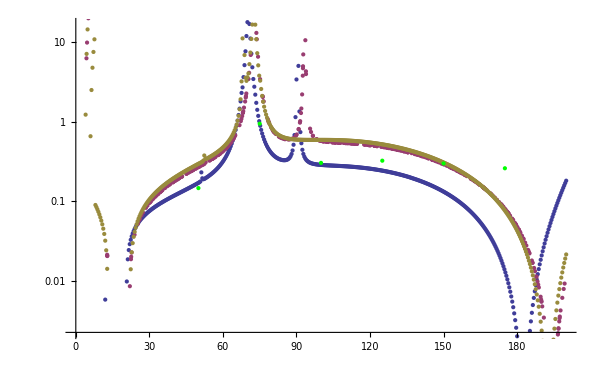

```mathematica
yaxel11=file1[[;;,4]];
yaxel31=file3[[;;,4]];
yaxel21=First@@@(Select[#,(Last@#=="b B"&&#[[2]]=="~o1 ~o1")&]&/@ file2[[;;,7]]);
Show[
ListLogPlot[
{Transpose@{xaxel1,yaxel11},
Transpose@{xaxel2,yaxel21},
Transpose@{xaxel3,yaxel31}},
ImageSize->{600,400}],
(*Graphics@Line[{{0,Log@0.3},{200,Log@0.3}}],
Graphics@Line[{{150,Log@0.002},{150,Log@10}}],*)
Graphics@{PointSize[Large],Green,Point@{175,Log@0.261}},
Graphics@{PointSize[Large],Green,Point@{150,Log@0.3}},
Graphics@{PointSize[Large],Green,Point@{125,Log@0.325}},
Graphics@{PointSize[Large],Green,Point@{100,Log@0.305}},
Graphics@{PointSize[Large],Green,Point@{75,Log@0.948}},
Graphics@{PointSize[Large],Green,Point@{50,Log@0.147}}]
```

HH

First::argx: First called with 0 arguments; 1 argument is expected.

General::stop: Further output of First :: argx will be suppressed during this calculation.

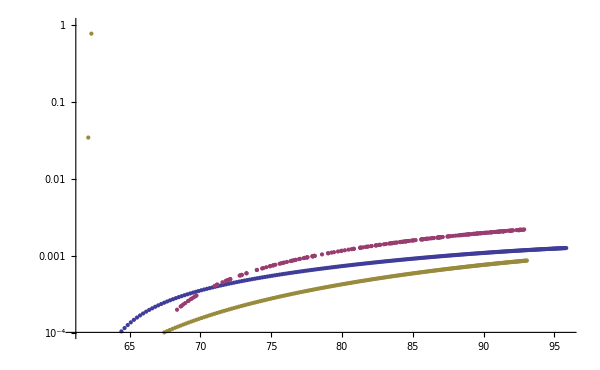

```mathematica
yaxel12=file1[[;;,6]];
yaxel32=file3[[;;,6]];
yaxel22=2First@@@(Select[#,(Last@#=="h1 h1"&&#[[2]]=="~o1 ~o1")&]&/@ file2[[;;,7]]);
ListLogPlot[{Transpose@{xaxel1,yaxel12},Transpose@{xaxel2,yaxel22},Transpose@{xaxel3,yaxel32}},ImageSize->{600,400}]
```

WW

First::argx: First called with 0 arguments; 1 argument is expected.

General::stop: Further output of First :: argx will be suppressed during this calculation.

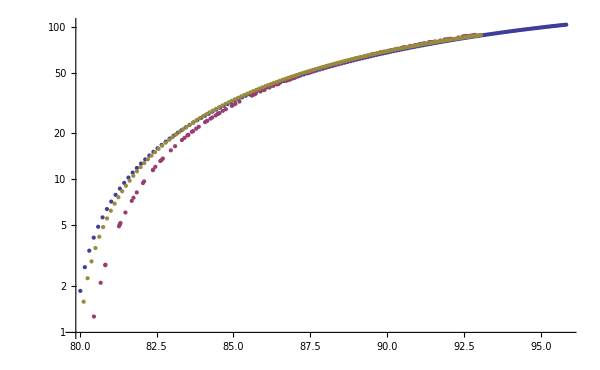

```mathematica
yaxel13=file1[[;;,7]];
yaxel33=file3[[;;,7]];
yaxel23=First@@@(Select[#,(Last@#=="W+ W-"&&#[[2]]=="~o1 ~o1")&]&/@ file2[[;;,7]]);
ListLogPlot[{Transpose@{xaxel1,yaxel13},Transpose@{xaxel2,yaxel23},Transpose@{xaxel3,yaxel33}},ImageSize->{600,400}]
```

ZZ

First::argx: First called with 0 arguments; 1 argument is expected.

General::stop: Further output of First :: argx will be suppressed during this calculation.

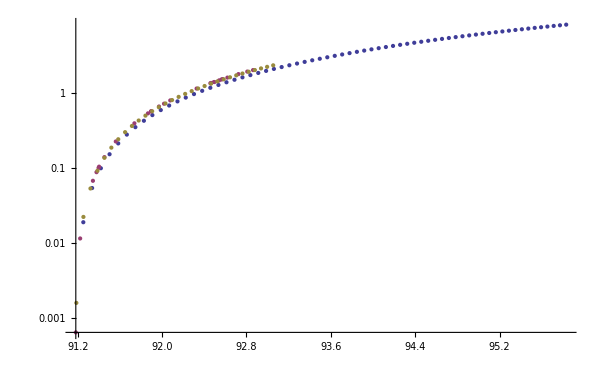

```mathematica
yaxel14=file1[[;;,8]];
yaxel34=file3[[;;,8]];
yaxel24=First@@@(Select[#,(Last@#=="Z Z"&&#[[2]]=="~o1 ~o1")&]&/@ file2[[;;,7]]);
ListLogPlot[{Transpose@{xaxel1,yaxel14},Transpose@{xaxel2,yaxel24},Transpose@{xaxel3,yaxel34}},ImageSize->{600,400}]
```

```mathematica
z
```